```mathematica
ftest = Function[t,Piecewise[{{0,t<0},{1/2,t<1/2},{3/2,t<1},{0,True}}]]
```

Function[t,Piecewise[{{0, t<0}, {1/2, t<1/2}, {3/2, t<1}, {0, True}}]]

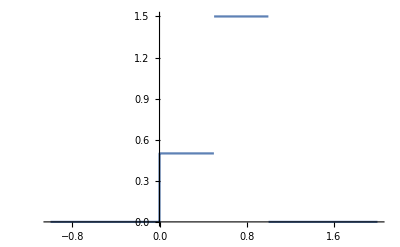

```mathematica
Plot[ftest[t],{t,-1,2}]
```

```mathematica
ftest2[t_]:=Piecewise[{{0,t<0},{1/2,t<1/2},{3/2,t<1},{0,True}}]
```

```mathematica
ftest2[tt][[2]]//FullForm
```

0

```mathematica
ftest[tt][[1]]//FullForm
```

List[List[0,Less[tt,0]],List[Rational[1,2],Less[tt,Rational[1,2]]],List[Rational[3,2],Less[tt,1]]]

```mathematica
sflist={{0,0},{1/2,1/2},{3/2,1}};
```

```mathematica
pcListToFunction[pcl_]:=Function[t,Evaluate[Piecewise[{#[[1]],t<#[[2]]}&/@pcl,0]]]
```

```mathematica
pcListToFunction[sflist]
```

Function[t$,Piecewise[{{0, t$<0}, {1/2, t$<1/2}, {3/2, t$<1}, {0, True}}]]

```mathematica
Plot[pcListToFunction[sflist][t],{t,-1,2}]
```

-Graphics-

```mathematica
AAA.BBB//FullForm
```

Dot[AAA,BBB]